```mathematica
Needs["NoisyQuantumTeleportationBenchmarking`", "C:/Users/pdbru/Desktop/tesis/mathematica/NoisyQuantumTeleportationBenchmarking.wl"]
```

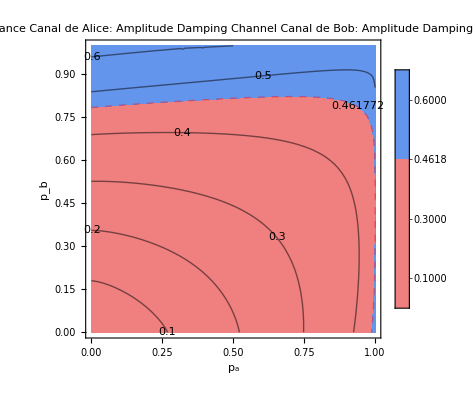

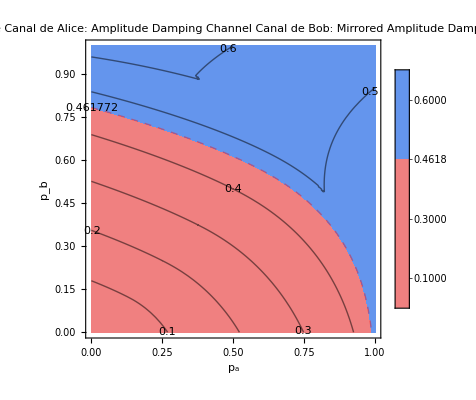

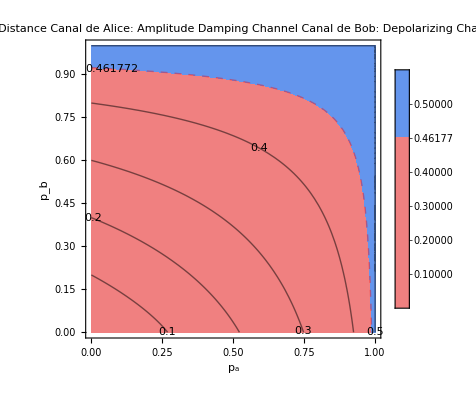

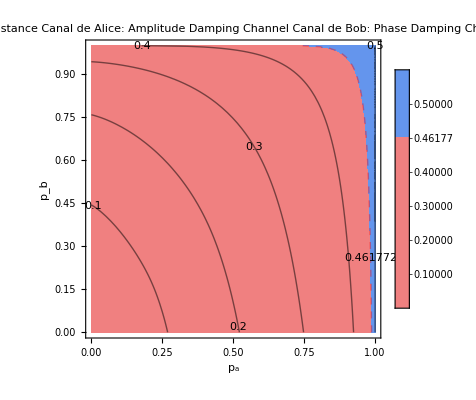

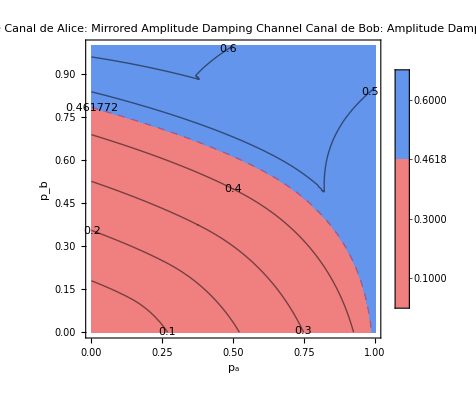

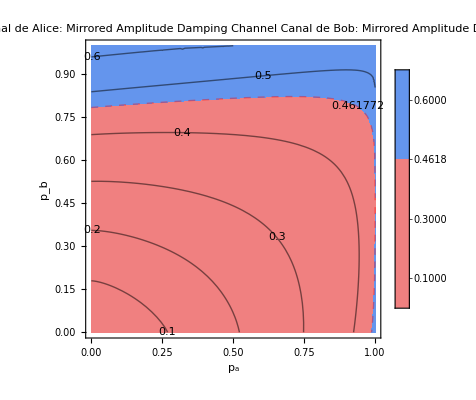

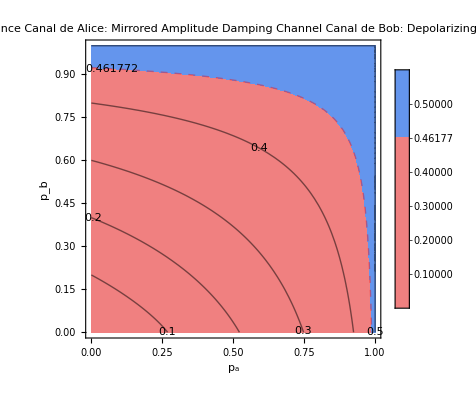

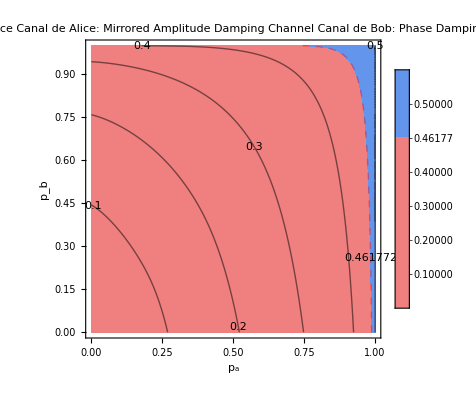

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«30 more identical outputs»

```mathematica
ForAllChannelsAndDistances[Function[{chA, chB, d, AvgDist, PaulisAvg}, 
newStyle[x_]:=x/. l_Line:>Sequence[Opacity[.4],Thick,Dashed,Red,l];

th = GetDistanceThreshold[d];
color[h_/;h<th]:=ColorData["HTML","LightCoral"];
     color[h_/;h≥th]:=ColorData["HTML","CornflowerBlue"];
cTr=ContourPlot[AvgTr[pA,pB],{pA,0,1},{pB,0,1},Contours->Table[i,{i,0.1,0.6,0.05}],ContourLabels->True,AxesLabel->{"pA","pB"},ColorFunction->color,ColorFunctionScaling->False,MaxRecursion->3,Mesh->None];

Print[ContourPlot[AvgDist[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> GetDistanceLabel[d] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB],
ColorFunction->color,ColorFunctionScaling->False,MaxRecursion->3,Mesh->None
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th]]

(*Print[GraphicsRow[{
ContourPlot[AvgDist[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> GetDistanceLabel[d] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB],
ImageSize->400,ColorFunction->color,ColorFunctionScaling->False,MaxRecursion->3,Mesh->None
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th], 
ContourPlot[PaulisAvg[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], th]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> GetDistanceLabel[d] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB]<> "\nPauli Average" ,
ImageSize->400,ColorFunction->color,ColorFunctionScaling->False,MaxRecursion->3,Mesh->None
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th], 
ContourPlot[Abs[PaulisAvg[pA,pB] - AvgDist[pA,pB]],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
PlotLegends->Automatic, 
PlotLabel-> GetDistanceLabel[d] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB]<> "\nAbsolute averages difference",
ImageSize->400
]
}, 0, ImageSize->Full]];*)
]]
```